```mathematica
f[x_]:=Cos[2 Pi x];
range={-1, 1, .1};
```

```mathematica
r1=range[[1]];r2=range[[2]];T=range[[3]];
Sx=f/@(Range@@range);
```

```mathematica
Round[Sx, .001]
Fourier[Sx]
Round[InverseFourier[%], .001]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{4.58258,2.6958×10^-16,2.12382×10^-16,1.35765×10^-16,6.1274×10^-17,8.32434×10^-18,-1.19672×10^-17,0.,3.31114×10^-17,7.00182×10^-17,9.36852×10^-17,9.36852×10^-17,7.00182×10^-17,3.31114×10^-17,0.,-1.19672×10^-17,8.32434×10^-18,6.1274×10^-17,1.35765×10^-16,2.12382×10^-16,2.6958×10^-16}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
sincn[x_]:=N[Sin[Pi x]/(Pi x)]
```

```mathematica
xA[Sx_][t_]:=Dot[Sx,Table[ sincn[(t-n )/T], {n, r1, r2 ,T}]]
```

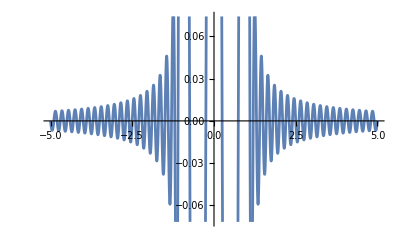

```mathematica
rr=RandomReal[{0, 1}, {Length[Sx]}];
Show[Plot[xA[Sx][t], {t, -5, 5}], ListPlot[Transpose[{Range@@range, Sx}]]]
```

```mathematica
errSum[Sx_]:=Sum[(f[x]-xA[Sx][xA[Sx][x]])^2, {x, r1, r2, T}]
```

```mathematica
Plot3D[errSum[{w1,w2}], {w1, -1, 1}, {w2, -1, 1}]
```

-Graphics3D-

```mathematica
n=2;
s=NMinimize[errSum[Table[x[i], {i, n}]], Table[x[i], {i, n}]]
```

NMinimize::nnum: The function value (1.-3.89817×10^-17 (-1.)[1]+3.89817×10^-17 (-1.)[2])^2+(0.809017-3.89817×10^-17 (-0.9)[1]+3.89817×10^-17 (-0.9)[2])^2+(0.309017-«1»+«24» «1»)^2+(«1»)^2+(«1»)^2+«11»+(«1»)^2+(«1»)^2+(1.-«1»+«24» «1»)^2+(0.809017-(«1»)/(-2.+«1»)-(«1»)/(-1.«1»10.«1»«20»«1»«1»]))^2+(0.309017-(0.31831 «1» Sin[«18» («1»)])/(-2.+10. 0.2[«1»])-(0.31831 0.2[1] Sin[3.14159 (-1.+Times[«2»])])/(-1.+10. 0.2[«1»]))^2 is not a number at {x[1],x[2]} = {0.918621,0.716689}.

NMinimize[(1.-(0.31831 (-1.)[2] Sin[3.14159 (-2.+10. (1.41788×10^-16 (-1.)[1.]-3.89817×10^-17 (-1.)[2.]))])/(-2.+10. (1.41788×10^-16 (-1.)[1.]-3.89817×10^-17 (-1.)[2.]))-(0.31831 (-1.)[1] Sin[3.14159 (-1.+10. (1.41788×10^-16 (-1.)[1.]-3.89817×10^-17 (-1.)[2.]))])/(-1.+10. (1.41788×10^-16 (-1.)[1.]-3.89817×10^-17 (-1.)[2.])))^2+(0.809017-(0.31831 (-0.9)[2] Sin[3.14159 (-2.+10. (-3.89817×10^-17 (-0.9)[1.]+1.41788×10^-16 (-0.9)[2.]))])/(-2.+10. (-3.89817×10^-17 (-0.9)[1.]+1.41788×10^-16 (-0.9)[2.]))-(0.31831 (-0.9)[1] Sin[3.14159 (-1.+10. (-3.89817×10^-17 (-0.9)[1.]+1.41788×10^-16 (-0.9)[2.]))])/(-1.+10. (-3.89817×10^-17 (-0.9)[1.]+1.41788×10^-16 (-0.9)[2.])))^2+(0.309017-(0.31831 (-0.8)[2] Sin[3.14159 (-2.+10. (3.89817×10^-17 (-0.8)[1.]-3.89817×10^-17 (-0.8)[2.]))])/(-2.+10. (3.89817×10^-17 (-0.8)[1.]-3.89817×10^-17 (-0.8)[2.]))-(0.31831 (-0.8)[1] Sin[3.14159 (-1.+10. (3.89817×10^-17 (-0.8)[1.]-3.89817×10^-17 (-0.8)[2.]))])/(-1.+10. (3.89817×10^-17 (-0.8)[1.]-3.89817×10^-17 (-0.8)[2.])))^2+(-0.309017-(0.31831 (-0.7)[2] Sin[3.14159 (-2.+10. (-3.89817×10^-17 (-0.7)[1.]+3.89817×10^-17 (-0.7)[2.]))])/(-2.+10. (-3.89817×10^-17 (-0.7)[1.]+3.89817×10^-17 (-0.7)[2.]))-(0.31831 (-0.7)[1] Sin[3.14159 (-1.+10. (-3.89817×10^-17 (-0.7)[1.]+3.89817×10^-17 (-0.7)[2.]))])/(-1.+10. (-3.89817×10^-17 (-0.7)[1.]+3.89817×10^-17 (-0.7)[2.])))^2+(-0.809017-(0.31831 (-0.6)[2] Sin[3.14159 (-2.+10. (3.89817×10^-17 (-0.6)[1.]-3.89817×10^-17 (-0.6)[2.]))])/(-2.+10. (3.89817×10^-17 (-0.6)[1.]-3.89817×10^-17 (-0.6)[2.]))-(0.31831 (-0.6)[1] Sin[3.14159 (-1.+10. (3.89817×10^-17 (-0.6)[1.]-3.89817×10^-17 (-0.6)[2.]))])/(-1.+10. (3.89817×10^-17 (-0.6)[1.]-3.89817×10^-17 (-0.6)[2.])))^2+(-1.-(0.31831 (-0.5)[2] Sin[3.14159 (-2.+10. (-3.89817×10^-17 (-0.5)[1.]+3.89817×10^-17 (-0.5)[2.]))])/(-2.+10. (-3.89817×10^-17 (-0.5)[1.]+3.89817×10^-17 (-0.5)[2.]))-(0.31831 (-0.5)[1] Sin[3.14159 (-1.+10. (-3.89817×10^-17 (-0.5)[1.]+3.89817×10^-17 (-0.5)[2.]))])/(-1.+10. (-3.89817×10^-17 (-0.5)[1.]+3.89817×10^-17 (-0.5)[2.])))^2+(-0.809017-(0.31831 (-0.4)[2] Sin[3.14159 (-2.+10. (2.65154×10^-16 (-0.4)[1.]-2.27459×10^-16 (-0.4)[2.]))])/(-2.+10. (2.65154×10^-16 (-0.4)[1.]-2.27459×10^-16 (-0.4)[2.]))-(0.31831 (-0.4)[1] Sin[3.14159 (-1.+10. (2.65154×10^-16 (-0.4)[1.]-2.27459×10^-16 (-0.4)[2.]))])/(-1.+10. (2.65154×10^-16 (-0.4)[1.]-2.27459×10^-16 (-0.4)[2.])))^2+(-0.309017-(0.31831 (-0.3)[2] Sin[3.14159 (-2.+10. (-3.21698×10^-16 (-0.3)[1.]+2.65154×10^-16 (-0.3)[2.]))])/(-2.+10. (-3.21698×10^-16 (-0.3)[1.]+2.65154×10^-16 (-0.3)[2.]))-(0.31831 (-0.3)[1] Sin[3.14159 (-1.+10. (-3.21698×10^-16 (-0.3)[1.]+2.65154×10^-16 (-0.3)[2.]))])/(-1.+10. (-3.21698×10^-16 (-0.3)[1.]+2.65154×10^-16 (-0.3)[2.])))^2+(0.309017-(0.31831 (-0.2)[2] Sin[3.14159 (-2.+10. (2.27459×10^-16 (-0.2)[1.]-1.8034×10^-16 (-0.2)[2.]))])/(-2.+10. (2.27459×10^-16 (-0.2)[1.]-1.8034×10^-16 (-0.2)[2.]))-(0.31831 (-0.2)[1] Sin[3.14159 (-1.+10. (2.27459×10^-16 (-0.2)[1.]-1.8034×10^-16 (-0.2)[2.]))])/(-1.+10. (2.27459×10^-16 (-0.2)[1.]-1.8034×10^-16 (-0.2)[2.])))^2+(0.809017-(0.31831 (-0.1)[2] Sin[3.14159 (-2.+10. (-1.8034×10^-16 (-0.1)[1.]+3.89817×10^-17 (-0.1)[2.]))])/(-2.+10. (-1.8034×10^-16 (-0.1)[1.]+3.89817×10^-17 (-0.1)[2.]))-(0.31831 (-0.1)[1] Sin[3.14159 (-1.+10. (-1.8034×10^-16 (-0.1)[1.]+3.89817×10^-17 (-0.1)[2.]))])/(-1.+10. (-1.8034×10^-16 (-0.1)[1.]+3.89817×10^-17 (-0.1)[2.])))^2+(1.-(0.31831 0.[2] Sin[3.14159 (-2.+10. (3.89817×10^-17 0.[1.]-3.89817×10^-17 0.[2.]))])/(-2.+10. (3.89817×10^-17 0.[1.]-3.89817×10^-17 0.[2.]))-(0.31831 0.[1] Sin[3.14159 (-1.+10. (3.89817×10^-17 0.[1.]-3.89817×10^-17 0.[2.]))])/(-1.+10. (3.89817×10^-17 0.[1.]-3.89817×10^-17 0.[2.])))^2+(0.809017-(0.31831 0.1[2] Sin[3.14159 (-2.+10. (1. 0.1[1.]+8.8713×10^-16 0.1[2.]))])/(-2.+10. (1. 0.1[1.]+8.8713×10^-16 0.1[2.]))-(0.31831 0.1[1] Sin[3.14159 (-1.+10. (1. 0.1[1.]+8.8713×10^-16 0.1[2.]))])/(-1.+10. (1. 0.1[1.]+8.8713×10^-16 0.1[2.])))^2+(0.309017-(0.31831 0.2[2] Sin[3.14159 (-2.+10. (-1.79867×10^-15 0.2[1.]+1. 0.2[2.]))])/(-2.+10. (-1.79867×10^-15 0.2[1.]+1. 0.2[2.]))-(0.31831 0.2[1] Sin[3.14159 (-1.+10. (-1.79867×10^-15 0.2[1.]+1. 0.2[2.]))])/(-1.+10. (-1.79867×10^-15 0.2[1.]+1. 0.2[2.])))^2+(-0.309017-(0.31831 0.3[2] Sin[3.14159 (-2.+10. (2.43734×10^-16 0.3[1.]-3.85092×10^-16 0.3[2.]))])/(-2.+10. (2.43734×10^-16 0.3[1.]-3.85092×10^-16 0.3[2.]))-(0.31831 0.3[1] Sin[3.14159 (-1.+10. (2.43734×10^-16 0.3[1.]-3.85092×10^-16 0.3[2.]))])/(-1.+10. (2.43734×10^-16 0.3[1.]-3.85092×10^-16 0.3[2.])))^2+(-0.809017-(0.31831 0.4[2] Sin[3.14159 (-2.+10. (-5.2645×10^-16 0.4[1.]+8.09166×10^-16 0.4[2.]))])/(-2.+10. (-5.2645×10^-16 0.4[1.]+8.09166×10^-16 0.4[2.]))-(0.31831 0.4[1] Sin[3.14159 (-1.+10. (-5.2645×10^-16 0.4[1.]+8.09166×10^-16 0.4[2.]))])/(-1.+10. (-5.2645×10^-16 0.4[1.]+8.09166×10^-16 0.4[2.])))^2+(-1.-(0.31831 0.5[2] Sin[3.14159 (-2.+10. (-3.89817×10^-17 0.5[1.]+3.89817×10^-17 0.5[2.]))])/(-2.+10. (-3.89817×10^-17 0.5[1.]+3.89817×10^-17 0.5[2.]))-(0.31831 0.5[1] Sin[3.14159 (-1.+10. (-3.89817×10^-17 0.5[1.]+3.89817×10^-17 0.5[2.]))])/(-1.+10. (-3.89817×10^-17 0.5[1.]+3.89817×10^-17 0.5[2.])))^2+(-0.809017-(0.31831 0.6[2] Sin[3.14159 (-2.+10. (-1.87191×10^-16 0.6[1.]+2.43734×10^-16 0.6[2.]))])/(-2.+10. (-1.87191×10^-16 0.6[1.]+2.43734×10^-16 0.6[2.]))-(0.31831 0.6[1] Sin[3.14159 (-1.+10. (-1.87191×10^-16 0.6[1.]+2.43734×10^-16 0.6[2.]))])/(-1.+10. (-1.87191×10^-16 0.6[1.]+2.43734×10^-16 0.6[2.])))^2+(-0.309017-(0.31831 0.7[2] Sin[3.14159 (-2.+10. (3.37973×10^-16 0.7[1.]-3.00277×10^-16 0.7[2.]))])/(-2.+10. (3.37973×10^-16 0.7[1.]-3.00277×10^-16 0.7[2.]))-(0.31831 0.7[1] Sin[3.14159 (-1.+10. (3.37973×10^-16 0.7[1.]-3.00277×10^-16 0.7[2.]))])/(-1.+10. (3.37973×10^-16 0.7[1.]-3.00277×10^-16 0.7[2.])))^2+(0.309017-(0.31831 0.8[2] Sin[3.14159 (-2.+10. (3.89817×10^-17 0.8[1.]-3.89817×10^-17 0.8[2.]))])/(-2.+10. (3.89817×10^-17 0.8[1.]-3.89817×10^-17 0.8[2.]))-(0.31831 0.8[1] Sin[3.14159 (-1.+10. (3.89817×10^-17 0.8[1.]-3.89817×10^-17 0.8[2.]))])/(-1.+10. (3.89817×10^-17 0.8[1.]-3.89817×10^-17 0.8[2.])))^2+(0.809017-(0.31831 0.9[2] Sin[3.14159 (-2.+10. (2.43734×10^-16 0.9[1.]-2.84122×10^-16 0.9[2.]))])/(-2.+10. (2.43734×10^-16 0.9[1.]-2.84122×10^-16 0.9[2.]))-(0.31831 0.9[1] Sin[3.14159 (-1.+10. (2.43734×10^-16 0.9[1.]-2.84122×10^-16 0.9[2.]))])/(-1.+10. (2.43734×10^-16 0.9[1.]-2.84122×10^-16 0.9[2.])))^2+(1.-(0.31831 1.[2] Sin[3.14159 (-2.+10. (3.89817×10^-17 1.[1.]-3.89817×10^-17 1.[2.]))])/(-2.+10. (3.89817×10^-17 1.[1.]-3.89817×10^-17 1.[2.]))-(0.31831 1.[1] Sin[3.14159 (-1.+10. (3.89817×10^-17 1.[1.]-3.89817×10^-17 1.[2.]))])/(-1.+10. (3.89817×10^-17 1.[1.]-3.89817×10^-17 1.[2.])))^2,{x[1],x[2]}]